Datos del mundo real

Una característica central de Wolfram Language es que contiene una cantidad inmensa de datos del mundo real. Por ejemplo, datos sobre países, animales, películas y multitud de otras cosas. Todo ello proviene de la base de conocimientos Wolfram, Wolfram Knowledgebase, que se actualiza constantemente y que es también lo que alimenta a Wolfram|Alpha y todos los servicios ahí disponibles.

¿Cómo puede accederse a la información acerca de un país en Wolfram Language? La manera más sencilla de hacerlo es usando el inglés llano, ingresando la petición después de oprimir ctrl= (oprimir simultáneamente la tecla de Control y la de =), o bien, en el caso de estar usando un dispositivo táctil, después de oprimir el botón .

```mathematica
LinguisticAssistant
```

Ingrese la frase en inglés “united states”:

```mathematica
LinguisticAssistant
```

En cuanto se oprima return, Wolfram Language tratará de interpretar lo que se escribió. Si es el caso, se mostrará un recuadro amarillo que representa una entidad de Wolfram Language. Así, en este ejemplo, se trata de la entidad correspondiente a los Estados Unidos (United States).

```mathematica
LinguisticAssistant
```

Se oprime la casilla con la marca ✓ para confirmar la petición:

```mathematica
Entity["Country","UnitedStates"]
```

Y ahora ya se pueden hacer preguntas acerca de una diversidad de propiedades de esta entidad; entonces, poniendo por caso, la bandera estadounidense:

Encuentre la propiedad “bandera” de los Estados Unidos (United States):



```mathematica
Entity["Country","UnitedStates"]["Flag"]
```

Con el resultado así obtenido se puede continuar efectuando algún proceso que, en este caso, podría ser un procesamiento de imágenes.

Obtenga el negativo de color de la bandera estadounidense:

```mathematica
ColorNegate[-Graphics-]
```

-Graphics-

Si solo se quisiera obtener la bandera estadounidense, podría hacerse directamente en inglés.

```mathematica
LinguisticAssistant
```

-Graphics-

EntityValue es una forma más flexible de obtener el valor de alguna propiedad.

Use EntityValue para obtener la bandera de los Estados Unidos (United States):

```mathematica
EntityValue[Entity["Country","UnitedStates"],"Flag"]
```

-Graphics-

EntityValue también acepta listas de entidades.

Obtenga las banderas de una lista de países:

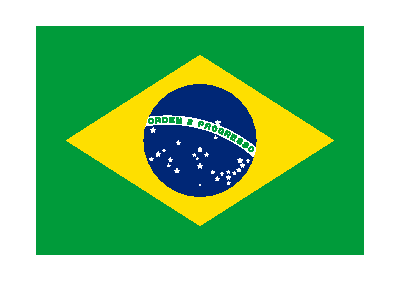

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[{Entity["Country","UnitedStates"],Entity["Country","Brazil"],Entity["Country","China"]},"Flag"]
```

Wolfram Language incorpora mucha información sobre países, así como de muchos otros temas.

Encuentre cuántas estaciones de radio hay en una lista de países:

```mathematica
EntityValue[{Entity["Country","UnitedStates"],Entity["Country","Brazil"],Entity["Country","China"]},"RadioStations"]
```

{13769,1822,673}

Haga una gráfica circular con el resultado:

```mathematica
PieChart[EntityValue[{Entity["Country","UnitedStates"],Entity["Country","Brazil"],Entity["Country","China"]},"RadioStations"]]
```

-Graphics-

Encuentre los países colindantes con Suiza (Switzerland):

```mathematica
Entity["Country","Switzerland"]["BorderingCountries"]
```

{Austria,France,Germany,Italy,Liechtenstein}

Pedir sus banderas:

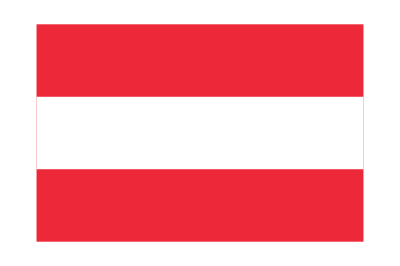


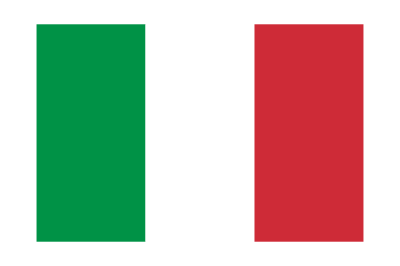
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[Entity["Country","Switzerland"]["BorderingCountries"],"Flag"]
```

A veces se desea acceder a una clase de entidades tales como planetas, por ejemplo.

Pregunte sobre planetas y obtenga la clase de entidades correspondiente a planetas:

```mathematica
LinguisticAssistant
```

planets

Se indican las clases de entidades con . Se obtiene la lista de todas las entidades de una clase usando EntityList.

Vea la lista de los planetas:

```mathematica
EntityList[EntityClass["Planet",All]]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

Vea imágenes de todos los planetas:

```mathematica
EntityValue[EntityClass["Planet",All],"Image"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

EntityValue puede manejar directamente clases de entidades, o sea que no se requiere usar EntityList.

Muestre el radio de cada planeta en forma de gráfica de barras:

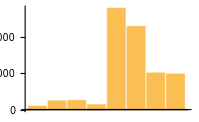

```mathematica
BarChart[EntityValue[EntityClass["Planet",All],"Radius"]]
```

Resulta muy conveniente el uso del inglés llano cuando quiere describirse algo. El problema es que puede dar lugar a ambigüedades: al decir “mercury”, ¿se está hablando del planeta Mercurio (Mercury), o del elemento químico mercurio (mercury), o de algo más también llamado “mercury” en inglés? Si se usa ctrl=, siempre se generará una respuesta inicial, y si se oprime el icono  se obtendrá otra diferente. Si se acepta alguna de ellas, hay que indicarlo presionando la casilla marcada  .

```mathematica
LinguisticAssistant
```

Para ver cómo se representan internamente las entidades en Wolfram Language, puede usarse InputForm.

Muestre la forma interna de la entidad que representa Estados Unidos (USA):

```mathematica
InputForm[LinguisticAssistant]
```

Entity["Country", "UnitedStates"]

Muestre la forma interna para la ciudad de Nueva York (abreviada como nyc):

```mathematica
InputForm[LinguisticAssistant]
```

Entity["City", {"NewYork", "NewYork", "UnitedStates"}]

Dentro de Wolfram Language hay millones de entidades, cada una de ellas con una forma interna definida. En principio, puede ingresar a cualquiera de ellas usando su forma interna aunque, a menos que se vaya a usar la misma entidad una y otra vez, es mucho más práctico usar sencillamente ctrl= y escribir su nombre en inglés llano.

Hay miles de diferentes tipos de entidades en Wolfram Language que cubren una gran variedad de áreas del conocimiento. Para saber más al respecto, hay que explorar la documentación de Wolfram Language, o las páginas de ejemplos en Wolfram|Alpha. Cada tipo de entidad tiene una lista de propiedades, y no es raro encontrar casos que tengan centenares de ellas. Una forma de acceder a esa lista es usando EntityProperties.

Las propiedades posibles para parques de diversiones:

```mathematica
EntityProperties["AmusementPark"]
```

{administrative division,type,area,city,closing date,country,image,latitude,longitude,name,number of rides,opening date,owner,coordinates,slogan,rides,status}

Sin embargo, en la práctica, una buena forma de proceder es preguntar en inglés llano sobre una propiedad determinada de alguna entidad, revisar la interpretación que se encontró y, a partir de ahí, volver a utilizar dicha propiedad.

Pregunte la altura de la torre Eiffel (Eiffel Tower):

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

1062.99 ft

Ahora se reutiliza la propiedad "Height" (altura), aplicada a la Gran Pirámide:

```mathematica
Entity["Building","GreatPyramidOfGiza::jbm66"]["Height"]
```

456.037 ft

Diferentes tipos de entidades tienen propiedades diferentes. Una que es común a muchos tipos de entidad es "Image".

Obtenga imágenes de diversas entidades:

```mathematica
Entity["Species","Species:PhascolarctosCinereus"]["Image"]
```

-Graphics-

```mathematica
Entity["Building","EiffelTower::5h9w8"]["Image"]
```

-Graphics-

```mathematica
Entity["Artwork","TheStarryNight::VincentVanGogh"]["Image"]
```

-Graphics-

```mathematica
Entity["Person","StephenWolfram::j276d"]["Image"]
```

-Graphics-

Otros tipos de objetos tienen otras propiedades diferentes.

Gráfica de una molécula de cafeína:

```mathematica
Entity["Chemical","Caffeine"]["MoleculePlot"]
```

-Graphics-

Gráfica rotativa en 3D de una calavera:

```mathematica
Entity["AnatomicalStructure","Skull"]["Graphics3D"]
```

-Graphics-

Una red que se dobla para formar el logo en 3D de nuestra compañía:

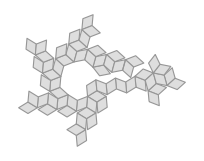

```mathematica
Entity["Polyhedron","RhombicHexecontahedron"]["NetImage"]
```

Vocabulario

ctrl=   |   | entrada en inglés llano
EntityList[class] |   | entidades en una clase 
EntityValue[entities,property] |   | valor de una de las propiedades de alguna entidad 
EntityProperties[type] |   | lista de las propiedades de un tipo de entidad 
InputForm[entity] |   | representación interna en Wolfram Language de una entidad

"13 Exercises Available"
"with 3 extras" | "Get Started »"

Encuentre la bandera de Suiza (Switzerland). »

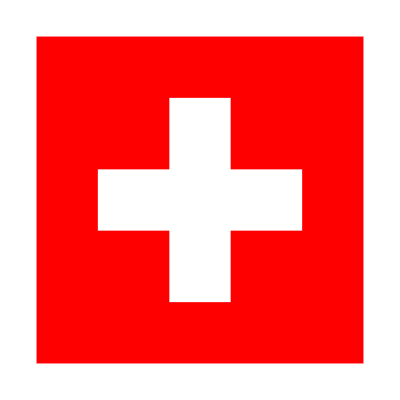
| Expected output: |  
  | -Graphics- |

Obtenga una imagen de un elefante. »

| Sample expected output: |  
  | -Graphics- |

Use la propiedad "Mass" (masa) para generar una lista de las masas de los planetas. »

| Expected output: |  
  | {3.30104×10^23 "kg",4.86732×10^24 "kg",5.9721986×10^24 "kg",6.41693×10^23 "kg",1.89813×10^27 "kg",5.68319×10^26 "kg",8.68103×10^25 "kg",1.0241×10^26 "kg"} |

Cree una gráfica de barras de las masas de los planetas. »

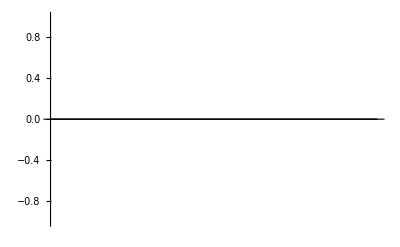
| Expected output: |  
  | -Graphics- |

Haga un collage con las imágenes de los planetas. »

| Expected output: |  
  | -Graphics- |

Detecte los bordes de la bandera de China. »

| Expected output: |  
  | -Graphics- |

Encuentre la altura del edificio Empire State (Empire State Building). »

| Expected output: |  
  | 1250. "ft" |

Calcule la altura del edificio Empire State dividida por la altura de la Gran Pirámide (Great Pyramid). »

| Expected output: |  
  | 2.74101 |

Calcule la elevación del monte Everest (Mount Everest) dividida por la altura del edificio Empire State. »

| Expected output: |  
  | 23.2231 |

Encuentre los colores dominantes en la pintura The Starry Night. »

| Expected output: |  
  | {RGBColor[0.2768655066668183, 0.3712643071964756, 0.5642037010622294],RGBColor[0.12012834022024377, 0.13444662562587364, 0.12819278684469784],RGBColor[0.589686385011058, 0.6392285324724452, 0.5548502694119095]} |

Encuentre los colores dominantes en un collage con las imágenes de las banderas de todos los países de Europa. »

| Expected output: |  
  | {RGBColor[0.8384380770968652, 0.10378446717897716, 0.18712551720692133],RGBColor[0.9930488857973235, 0.9885807188350121, 0.988462260402767],RGBColor[0.07144901267884562, 0.24438683922410798, 0.587652291734621],RGBColor[0.9744416667249923, 0.8004261361448077, 0.09438578646953585],RGBColor[0.1269646589300012, 0.5321736217747745, 0.2846829216683256]} |

Haga una gráfica circular de los PIB de los países de Europa (countries in Europe). »

| Expected output: |  
  | -Graphics- |

Sume la imagen de un koala con la imagen de la bandera de Australia. »

| Sample expected output: |  
  | -Graphics- |

Haga un collage con las banderas de todos los países de Europa, usando la propiedad "FlagImage". »

| Expected output: |  
  | -Graphics- |

Detecte los bordes en una imagen de la pintura The Starry Night. »

| Expected output: |  
  | -Graphics- |

Obtenga el negativo de color de la pintura Mona Lisa. »

| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿De dónde obtiene Wolfram Language sus datos del mundo real?

Todo proviene de Wolfram Knowledgebase (la base de conocimientos central de Wolfram Language). Este repositorio se ha venido construyendo a lo largo de muchos años, revisando y curando cuidadosamente los datos provenientes de miles de fuentes originales.

¿Se actualizan regularmente los datos en Wolfram Language?

Sí. Se hace un gran esfuerzo por mantenerlos actualizados. De hecho, hay nueva información incorporándose a cada segundo sobre precios de mercado, clima, terremotos, posiciones de aeronaves y muchas otras cosas.

¿Qué grado de precisión tienen los datos en Wolfram Language?

Se trabaja minuciosamente para que sean tan precisos como sea posible, y se chequean extensamente. Pero, a fin de cuentas, esto depende también de lo que reportan los gobiernos y otros organismos autónomos.

¿Qué relación tiene la información con la de Wolfram|Alpha?

Wolfram|Alpha utiliza la misma base de conocimientos que Wolfram Language.

¿Cómo hay que referirse a alguna entidad en particular?

En la forma que se desee. Wolfram Language está construido de tal modo que pueda comprender todas las maneras usuales de referirse a entidades (“New York City”, “NYC”, “the big apple”, etc., funcionan correctamente.)

¿Cómo se pueden encontrar todas las propiedades y valores de una entidad dada?

Use entity["Dataset"] o entity["PropertyAssociation"].

¿Qué significa una respuesta Missing[...] al preguntar por algún EntityValue?

Sencillamente que no se conoce la respuesta para el valor solicitado o, al menos, que no se encuentra en Wolfram Knowledgebase. Use DeleteMissing para desechar los elementos Missing[...] de una lista.

¿Puede un usuario generar sus propias entidades y añadirles sus propios datos?

Sí, utilizando EntityStore.

Notas técnicas

Wolfram Knowledgebase está guardada en la nube, así que, aun si se usa alguna versión de escritorio de Wolfram Language, habrá que estar conectado a la red si se quieren obtener datos del mundo real.

Wolfram Knowledgebase contiene muchos billones de datos y valores específicos, almacenados en un marco simbólico de Wolfram Language, con fundamento en una diversidad de tecnologías de bases de datos.

Wolfram Knowledgebase se ha construido y revisado sistemáticamente a partir de un gran número de fuentes de información primarias. No proviene de búsquedas en la web.

Por lo general, los datos del mundo real involucran unidades, que serán el tema de la siguiente sección.

En vez de usar lenguaje natural, se puede acceder a Wolfram Knowledgebase mediante funciones específicas tales como CountryData y MovieData. En ocasiones, esto puede ser más rápido.

Si se quiere conocer la fuente original de alguna información específica, puede buscarse en la documentación (ej. para CountryData, etc.), o bien buscarse la información en Wolfram|Alpha y seguir los vínculos a las fuentes.

En ocasiones, se quiere tratar con un caso especial de alguna entidad, como de un país en un año determinado, o cierta cantidad de una sustancia. Se puede lograr esto usando EntityInstance.

RandomEntity encuentra entidades al azar de un tipo dado.

Existe cierta simetría entre entidades y propiedades. entity[property] da el mismo resultado que property[entity]. Para obtener los valores de varias propiedades, úsese entity[{p_1,p_2,...}]; para obtener valores para varias entidades, úsese property[{e_1,e_2,...}]. (Obsérvese que para property[entity] se necesita el objeto de propiedad completo, tal como se obtiene con ctrl=, y no simplemente el nombre de la propiedad escrito como una cadena de caracteres).

Para explorar más

Áreas principales cubiertas por Wolfram Knowledgebase »

Información geográfica y computación »

Información científica, médica y computación »

Información sobre ingeniería y computación »

Información social, cultural y lingüística »